```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Oc={0,0,0,1};
Oc2={6,0,0,1};
zeta1 = -2;
zeta2=-1;
alpha=45;
beta = -45;
Oc2={6,0,0,1};
Rot1=RotationsE2[alpha];
Rot2=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
```

M of C2=(1/(√2) | 0 | -1/(√2) | -3 √2
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | -3 √2
0 | 0 | 0 | 1)

M2 of C1 =(1/(√2) | 0 | 1/(√2) | 0
0 | 1 | 0 | 0
-1/(√2) | 0 | 1/(√2) | 0
0 | 0 | 0 | 1)

ProjectionMtxCamera1(-√2 | 0 | -√2 | 0
0 | -2 | 0 | 0
√2 | 0 | -√2 | 0
-1/(√2) | 0 | 1/(√2) | 0)

ProjectionMtxCamera2(-1/(√2) | 0 | 1/(√2) | 3 √2
0 | -1 | 0 | 0
-1/(√2) | 0 | -1/(√2) | 3 √2
1/(√2) | 0 | 1/(√2) | -3 √2)

CameraProjectedPointsK1 = (√2 | -6 | 7 √2 | -3/(√2)-2 √2
-√2 | -6 | 9 √2 | -5/(√2)-2 √2
-√2 | -10 | 9 √2 | -5/(√2)-2 √2
√2 | -10 | 7 √2 | -3/(√2)-2 √2
3 √2 | -6 | 9 √2 | -3/(√2)-3 √2
√2 | -6 | 11 √2 | -5/(√2)-3 √2
√2 | -10 | 11 √2 | -5/(√2)-3 √2
3 √2 | -10 | 9 √2 | -3/(√2)-3 √2
-2 √2 | -16 | 14 √2 | -7 √2)

CameraProjectedPointsK2 = (-1/(√2) | -3 | 7/(√2) | -7/(√2)
-3/(√2) | -3 | 5/(√2) | -5/(√2)
-3/(√2) | -5 | 5/(√2) | -5/(√2)
-1/(√2) | -5 | 7/(√2) | -7/(√2)
-3/(√2) | -3 | 9/(√2) | -9/(√2)
-5/(√2) | -3 | 7/(√2) | -7/(√2)
-5/(√2) | -5 | 7/(√2) | -7/(√2)
-3/(√2) | -5 | 9/(√2) | -9/(√2)
-4 √2 | -8 | 2 √2 | -2 √2)

homogene CameraProjectedPointsK1 = ((√2)/(-3/(√2)-2 √2) | -6/(-3/(√2)-2 √2) | (7 √2)/(-3/(√2)-2 √2) | 1
-(√2)/(-5/(√2)-2 √2) | -6/(-5/(√2)-2 √2) | (9 √2)/(-5/(√2)-2 √2) | 1
-(√2)/(-5/(√2)-2 √2) | -10/(-5/(√2)-2 √2) | (9 √2)/(-5/(√2)-2 √2) | 1
(√2)/(-3/(√2)-2 √2) | -10/(-3/(√2)-2 √2) | (7 √2)/(-3/(√2)-2 √2) | 1
(3 √2)/(-3/(√2)-3 √2) | -6/(-3/(√2)-3 √2) | (9 √2)/(-3/(√2)-3 √2) | 1
(√2)/(-5/(√2)-3 √2) | -6/(-5/(√2)-3 √2) | (11 √2)/(-5/(√2)-3 √2) | 1
(√2)/(-5/(√2)-3 √2) | -10/(-5/(√2)-3 √2) | (11 √2)/(-5/(√2)-3 √2) | 1
(3 √2)/(-3/(√2)-3 √2) | -10/(-3/(√2)-3 √2) | (9 √2)/(-3/(√2)-3 √2) | 1
2/7 | (8 √2)/7 | -2 | 1)

homogene CameraProjectedPointsK2 = (1/7 | (3 √2)/7 | -1 | 1
3/5 | (3 √2)/5 | -1 | 1
3/5 | √2 | -1 | 1
1/7 | (5 √2)/7 | -1 | 1
1/3 | (√2)/3 | -1 | 1
5/7 | (3 √2)/7 | -1 | 1
5/7 | (5 √2)/7 | -1 | 1
1/3 | (5 √2)/9 | -1 | 1
2 | 2 √2 | -1 | 1)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

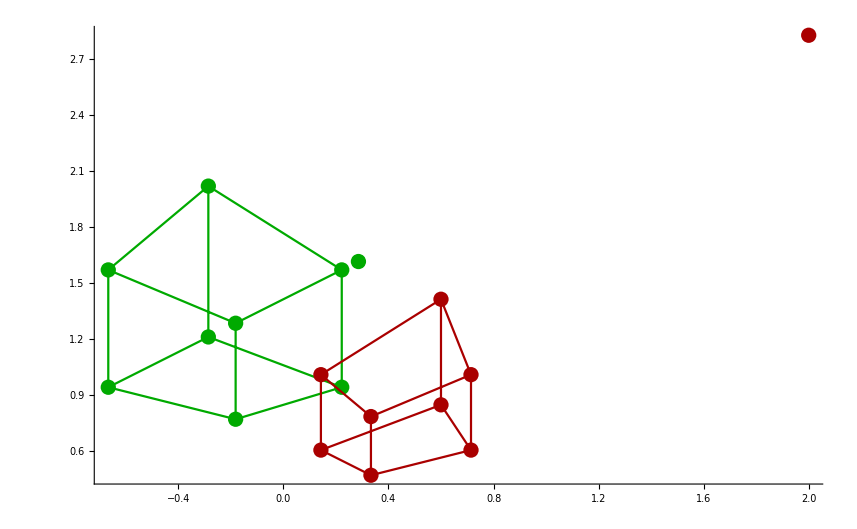

ImagePlaneC1Points = (-2/7 | (6 √2)/7 | 1
2/9 | (2 √2)/3 | 1
2/9 | (10 √2)/9 | 1
-2/7 | (10 √2)/7 | 1
-2/3 | (2 √2)/3 | 1
-2/11 | (6 √2)/11 | 1
-2/11 | (10 √2)/11 | 1
-2/3 | (10 √2)/9 | 1
2/7 | (8 √2)/7 | 1)

ImagePlaneC2Points = (1/7 | (3 √2)/7 | 1
3/5 | (3 √2)/5 | 1
3/5 | √2 | 1
1/7 | (5 √2)/7 | 1
1/3 | (√2)/3 | 1
5/7 | (3 √2)/7 | 1
5/7 | (5 √2)/7 | 1
1/3 | (5 √2)/9 | 1
2 | 2 √2 | 1)

CoefficientMtx = (-0.0408163 | 0.173169 | 0.142857 | -0.173169 | 0.734694 | 0.606092 | -0.285714 | 1.21218 | 1.
0.133333 | 0.565685 | 0.6 | 0.188562 | 0.8 | 0.848528 | 0.222222 | 0.942809 | 1.
0.133333 | 0.942809 | 0.6 | 0.31427 | 2.22222 | 1.41421 | 0.222222 | 1.57135 | 1.
-0.0408163 | 0.288615 | 0.142857 | -0.288615 | 2.04082 | 1.01015 | -0.285714 | 2.02031 | 1.
-0.222222 | 0.31427 | 0.333333 | -0.31427 | 0.444444 | 0.471405 | -0.666667 | 0.942809 | 1.
-0.12987 | 0.550992 | 0.714286 | -0.110198 | 0.467532 | 0.606092 | -0.181818 | 0.771389 | 1.
-0.12987 | 0.91832 | 0.714286 | -0.183664 | 1.2987 | 1.01015 | -0.181818 | 1.28565 | 1.
-0.222222 | 0.523783 | 0.333333 | -0.523783 | 1.23457 | 0.785674 | -0.666667 | 1.57135 | 1.
0.571429 | 3.23249 | 2. | 0.808122 | 4.57143 | 2.82843 | 0.285714 | 1.61624 | 1.)

RowReduce CoefficientMtx = [(1 | 0. | 0. | 0. | 0. | 0. | 0. | -6.95847×10^-16 | 0.
0 | 1 | 0. | 0. | 0. | 0. | 0. | -1. | 0.
0 | 0 | 1 | 0. | 0. | 0. | 0. | -9.65914×10^-16 | 0.
0 | 0 | 0 | 1 | 0. | 0. | 0. | -1. | 0.
0 | 0 | 0 | 0 | 1 | 0. | 0. | -1.88424×10^-16 | 0.
0 | 0 | 0 | 0 | 0 | 1 | 0. | 2. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 1 | 4.54801×10^-16 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)]

ns ={{5.66346×10^-17,0.377964,-1.79181×10^-16,0.377964,2.74047×10^-16,-0.755929,4.51834×10^-16,0.377964,4.48699×10^-16}}

F = (5.66346×10^-17 | 0.377964 | -1.79181×10^-16
0.377964 | 2.74047×10^-16 | -0.755929
4.51834×10^-16 | 0.377964 | 4.48699×10^-16)

lC1 = {{0.458162,-0.863919,0.458162},{0.356348,-0.671937,0.356348},{0.593914,-0.671937,0.593914},{0.763604,-0.863919,0.763604},{0.356348,-1.00791,0.356348},{0.291558,-0.82465,0.291558},{0.48593,-0.82465,0.48593},{0.593914,-1.00791,0.593914},{0.610883,-0.647939,0.610883}}

lPrimeC1 = {{0.229081,0.431959,-0.458162},{0.320713,0.604743,-0.641427},{0.534522,0.604743,-1.06904},{0.381802,0.431959,-0.763604},{0.178174,0.503953,-0.356348},{0.229081,0.647939,-0.458162},{0.381802,0.647939,-0.763604},{0.296957,0.503953,-0.593914},{1.06904,1.13389,-2.13809}}

e = {0.894427,-6.54413×10^-16,0.447214}

e' = {0.707107,-3.00549×10^-16,-0.707107}

EpipoleLines = (1. | -1.88562 | 1.
1. | -1.88562 | 1.
1. | -1.13137 | 1.
1. | -1.13137 | 1.
1. | -2.82843 | 1.
1. | -2.82843 | 1.
1. | -1.69706 | 1.
1. | -1.69706 | 1.
1. | -1.06066 | 1.)

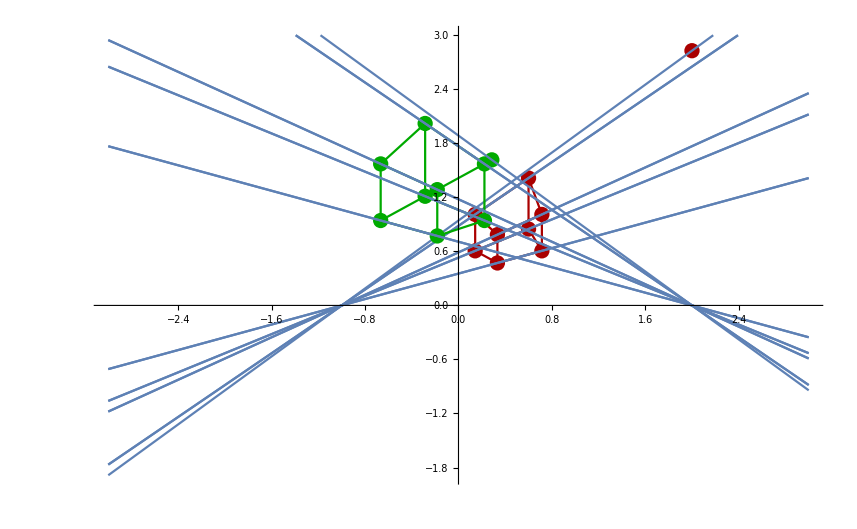

Start Rectification_________________________________________________________________________

z = {0,1,0}

wPrime = {0.707107,0.,0.707107}

w = {-0.447214,0.,0.894427}

wPrime = {1.,0.,1.}

w = {-0.5,0.,1.}

HpPrime = (1 | 0 | 0
0 | 1 | 0
1. | 0. | 1.)

Hp = (1 | 0 | 0
0 | 1 | 0
-0.5 | 0. | 1.)

ePrime inf = {0.707107,-3.00549×10^-16,0.}

e inf = {0.894427,-6.54413×10^-16,0.}

HrPrime = (0.755929 | -6.2788×10^-16 | 0
6.2788×10^-16 | 0.755929 | 0
0 | 0 | 1)

Hr = (0.377964 | -6.76184×10^-16 | 0
6.76184×10^-16 | 0.377964 | 4.48699×10^-16
0 | 0 | 1)

ePrimeHorizontal = {0.534522,2.16784×10^-16,0.}

eHorizontal = {0.338062,3.57452×10^-16,0.}

RecPointsC2 =(0.0944911 | 0.400892 | 1.
0.283473 | 0.400892 | 1.
0.283473 | 0.668153 | 1.
0.0944911 | 0.668153 | 1.
0.188982 | 0.267261 | 1.
0.31497 | 0.267261 | 1.
0.31497 | 0.445435 | 1.
0.188982 | 0.445435 | 1.)

RecPointsC1 =(-0.0944911 | 0.400892 | 1.
0.0944911 | 0.400892 | 1.
0.0944911 | 0.668153 | 1.
-0.0944911 | 0.668153 | 1.
-0.188982 | 0.267261 | 1.
-0.0629941 | 0.267261 | 1.
-0.0629941 | 0.445435 | 1.
-0.188982 | 0.445435 | 1.)

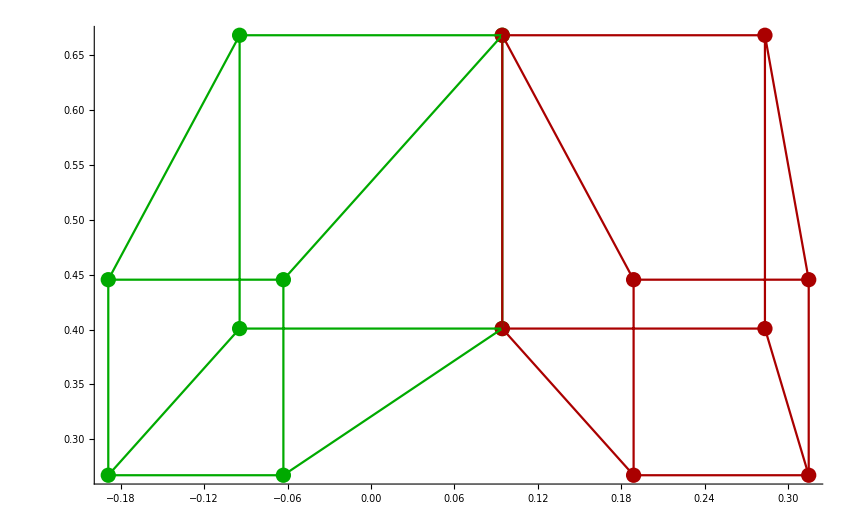

End Rectification___________________________________________________________________________

EMtx = {{1.13269×10^-16,0.755929,1.79181×10^-16},{0.755929,5.48094×10^-16,0.755929},{-9.03669×10^-16,-0.755929,4.48699×10^-16}}

U of E = {{-0.707107,-7.39568×10^-16,0.707107},{-9.42055×10^-16,1.,5.71452×10^-17},{0.707107,5.55112×10^-16,0.707107}}

Sigma of E = {{1.06904,0.,0.},{0.,1.06904,0.},{0.,0.,0.}}

V of E = {{-1.55431×10^-15,0.707107,-0.707107},{-1.,-1.29975×10^-15,6.33616×10^-16},{-4.62562×10^-16,0.707107,0.707107}}

S1 = (0. | 0.707107 | -1.30431×10^-16
-0.707107 | 0. | 0.707107
1.30431×10^-16 | -0.707107 | 0.)

S2 = (0. | -0.707107 | 1.30431×10^-16
0.707107 | 0. | -0.707107
-1.30431×10^-16 | 0.707107 | 0.)

R1 = (-1. | 6.27528×10^-16 | -1.55431×10^-15
8.47771×10^-16 | 1. | -1.63164×10^-16
-1.38778×10^-15 | 8.40838×10^-17 | 1.)

R2 = (-2.22045×10^-16 | 2.6854×10^-16 | 1.
-9.28586×10^-16 | -1. | 2.4398×10^-16
-1. | 8.11985×10^-16 | -2.77556×10^-16)

{{-1.,6.27528×10^-16,-1.55431×10^-15},{8.47771×10^-16,1.,-1.63164×10^-16},{-1.38778×10^-15,8.40838×10^-17,1.}} is no Rotation

{{-2.22045×10^-16,2.6854×10^-16,1.},{-9.28586×10^-16,-1.,2.4398×10^-16},{-1.,8.11985×10^-16,-2.77556×10^-16}} is no Rotation

Check if t of S1, S2 is equal = {{{0.707107,1.11022×10^-16,0.707107}},{{0.707107,1.11022×10^-16,0.707107}}}

t = {0.707107,1.11022×10^-16,0.707107}

P21  = (-2.22045×10^-16 | 2.6854×10^-16 | 1. | -0.707107
-9.28586×10^-16 | -1. | 2.4398×10^-16 | -1.11022×10^-16
-1. | 8.11985×10^-16 | -2.77556×10^-16 | -0.707107)

P22  = (-1. | 6.27528×10^-16 | -1.55431×10^-15 | -0.707107
8.47771×10^-16 | 1. | -1.63164×10^-16 | -1.11022×10^-16
-1.38778×10^-15 | 8.40838×10^-17 | 1. | -0.707107)

P23  = (-2.22045×10^-16 | 2.6854×10^-16 | 1. | 0.707107
-9.28586×10^-16 | -1. | 2.4398×10^-16 | 1.11022×10^-16
-1. | 8.11985×10^-16 | -2.77556×10^-16 | 0.707107)

P24  = (-1. | 6.27528×10^-16 | -1.55431×10^-15 | 0.707107
8.47771×10^-16 | 1. | -1.63164×10^-16 | 1.11022×10^-16
-1.38778×10^-15 | 8.40838×10^-17 | 1. | 0.707107)

Triangulation: WorldPoint reconstruction ___________________________________________________

C2Oc2 = {-0.707107,-1.11022×10^-16,-0.707107}

Ro2 = (-2.22045×10^-16 | -9.28586×10^-16 | -1.
2.6854×10^-16 | -1. | 8.11985×10^-16
1. | 2.4398×10^-16 | -2.77556×10^-16)

WOc2 = {-0.707107,6.53024×10^-16,0.707107}

ImagePlanePoints2 =(0.292893 | -0.606092 | 0.849964 | 1.
0.292893 | -0.848528 | 1.30711 | 1.
0.292893 | -1.41421 | 1.30711 | 1.
0.292893 | -1.01015 | 0.849964 | 1.
0.292893 | -0.471405 | 1.04044 | 1.
0.292893 | -0.606092 | 1.42139 | 1.
0.292893 | -1.01015 | 1.42139 | 1.
0.292893 | -0.785674 | 1.04044 | 1.
0.292893 | -2.82843 | 2.70711 | 1.)

ImagePlanePoints1 =(-2/7 | (6 √2)/7 | -2 | 1
2/9 | (2 √2)/3 | -2 | 1
2/9 | (10 √2)/9 | -2 | 1
-2/7 | (10 √2)/7 | -2 | 1
-2/3 | (2 √2)/3 | -2 | 1
-2/11 | (6 √2)/11 | -2 | 1
-2/11 | (10 √2)/11 | -2 | 1
-2/3 | (10 √2)/9 | -2 | 1
2/7 | (8 √2)/7 | -2 | 1)

LinesC1 = {{(√2)/(-3/(√2)-2 √2)+(√2 t)/(-3/(√2)-2 √2),-6/(-3/(√2)-2 √2)-(6 t)/(-3/(√2)-2 √2),-2-2 t},{-(√2)/(-5/(√2)-2 √2)-(√2 t)/(-5/(√2)-2 √2),-6/(-5/(√2)-2 √2)-(6 t)/(-5/(√2)-2 √2),-2-2 t},{-(√2)/(-5/(√2)-2 √2)-(√2 t)/(-5/(√2)-2 √2),-10/(-5/(√2)-2 √2)-(10 t)/(-5/(√2)-2 √2),-2-2 t},{(√2)/(-3/(√2)-2 √2)+(√2 t)/(-3/(√2)-2 √2),-10/(-3/(√2)-2 √2)-(10 t)/(-3/(√2)-2 √2),-2-2 t},{(3 √2)/(-3/(√2)-3 √2)+(3 √2 t)/(-3/(√2)-3 √2),-6/(-3/(√2)-3 √2)-(6 t)/(-3/(√2)-3 √2),-2-2 t},{(√2)/(-5/(√2)-3 √2)+(√2 t)/(-5/(√2)-3 √2),-6/(-5/(√2)-3 √2)-(6 t)/(-5/(√2)-3 √2),-2-2 t},{(√2)/(-5/(√2)-3 √2)+(√2 t)/(-5/(√2)-3 √2),-10/(-5/(√2)-3 √2)-(10 t)/(-5/(√2)-3 √2),-2-2 t},{(3 √2)/(-3/(√2)-3 √2)+(3 √2 t)/(-3/(√2)-3 √2),-10/(-3/(√2)-3 √2)-(10 t)/(-3/(√2)-3 √2),-2-2 t},{2/7+(2 t)/7,(8 √2)/7+(8 √2 t)/7,-2-2 t}}

LinesC2 = {{0.292893+1. t2,-0.606092-0.606092 t2,0.849964+0.142857 t2},{0.292893+1. t2,-0.848528-0.848528 t2,1.30711+0.6 t2},{0.292893+1. t2,-1.41421-1.41421 t2,1.30711+0.6 t2},{0.292893+1. t2,-1.01015-1.01015 t2,0.849964+0.142857 t2},{0.292893+1. t2,-0.471405-0.471405 t2,1.04044+0.333333 t2},{0.292893+1. t2,-0.606092-0.606092 t2,1.42139+0.714286 t2},{0.292893+1. t2,-1.01015-1.01015 t2,1.42139+0.714286 t2},{0.292893+1. t2,-0.785674-0.785674 t2,1.04044+0.333333 t2},{0.292893+1. t2,-2.82843-2.82843 t2,2.70711+2. t2}}

t & t2 = {t→-1.41248,t2→-0.175042,t→-1.53033,t2→-0.410744,t→-1.53033,t2→-0.410744,t→-1.41248,t2→-0.175042,t→-1.53033,t2→0.0606602,t→-1.64818,t2→-0.175042,t→-1.64818,t2→-0.175042,t→-1.53033,t2→0.0606602,t→-1.82496,t2→-0.528595}

ReconstructedPointsC1 = ((0.117851
-0.5
0.824958)
(-0.117851
-0.5
1.06066)
(-0.117851
-0.833333
1.06066)
(0.117851
-0.833333
0.824958)
(0.353553
-0.5
1.06066)
(0.117851
-0.5
1.29636)
(0.117851
-0.833333
1.29636)
(0.353553
-0.833333
1.06066))

ReconstructedPointsC2 = ((0.117851
-0.5
0.824958)
(-0.117851
-0.5
1.06066)
(-0.117851
-0.833333
1.06066)
(0.117851
-0.833333
0.824958)
(0.353553
-0.5
1.06066)
(0.117851
-0.5
1.29636)
(0.117851
-0.833333
1.29636)
(0.353553
-0.833333
1.06066))

scaleValueC1 = {-8.48528}

ResizedPointsC1 = {{{{-1.},{4.24264},{-7.}}},{{{1.},{4.24264},{-9.}}},{{{1.},{7.07107},{-9.}}},{{{-1.},{7.07107},{-7.}}},{{{-3.},{4.24264},{-9.}}},{{{-1.},{4.24264},{-11.}}},{{{-1.},{7.07107},{-11.}}},{{{-3.},{7.07107},{-9.}}}}

scaleValueC2 = {-8.48528}

ResizedPointsC2 = {{{{-1.},{4.24264},{-7.}}},{{{1.},{4.24264},{-9.}}},{{{1.},{7.07107},{-9.}}},{{{-1.},{7.07107},{-7.}}},{{{-3.},{4.24264},{-9.}}},{{{-1.},{4.24264},{-11.}}},{{{-1.},{7.07107},{-11.}}},{{{-3.},{7.07107},{-9.}}}}

GPC1={{-1.,4.24264},{1.,4.24264},{1.,7.07107},{-1.,7.07107},{-3.,4.24264},{-1.,4.24264},{-1.,7.07107},{-3.,7.07107}}

GPC2={{-1.,4.24264},{1.,4.24264},{1.,7.07107},{-1.,7.07107},{-3.,4.24264},{-1.,4.24264},{-1.,7.07107},{-3.,7.07107}}

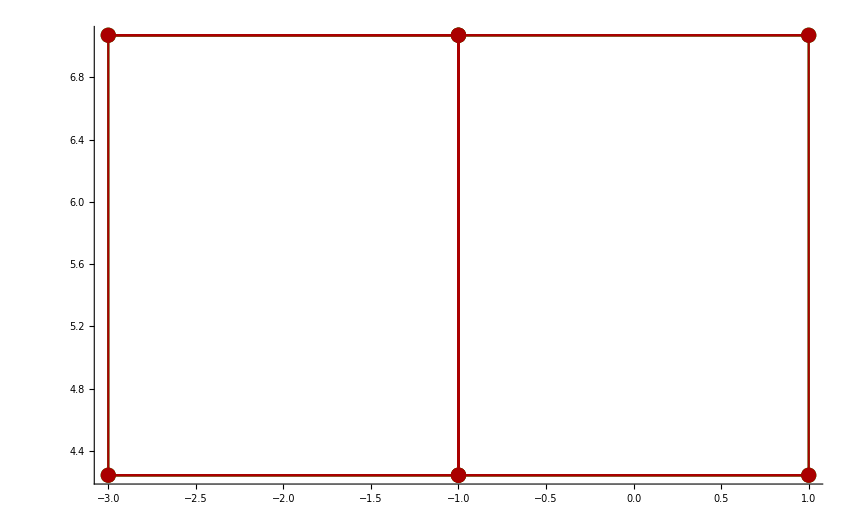

```mathematica
StartComputation[];
```